## Subradiance-protected excitation spreading for collimated photon emission

P. Huft
See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

How does my H_eff “know” that atomic transitions with circular light are possible? there is no defined quantization axis... maybe there should be? but then there would be zeeman splitting, which i don’t want. As it stands, all of the symmetric basis states for my diagonalized H_eff have equal occupation in all m=0 sub-states.

### Todo

- add code for saving the solutions to a text file; i do not want to have to reproduce these when some take several hours to evaluate.
-  Check: does the ferromagnetic eigenmode not fully overlap a true ferromagnetic mode? In other words, does it have polarizations near zero that would allow out-of-plane emission? The in-plane mode is never very subradiant for this reason. It may be that there is an eigenmode that is very nearly a perfect ferromagnetic configuration. 
- What mechanism is behind the superradiant spike around d = λ?

Restricting this problem to the single-excitation subspace, the Hamiltonian matrix elements are: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), ℏ=1, where μ,ν specify polarization in a spherical basis and j,k are the atom indices in the 2D grid. The dynamics in this subspace are coherent, but H is non-Hermitian, so there is dissipation as the excitation diffuses into the collective ground state.

- Δ,γ values used are arbitrary with the given choice of plot units.

## setup

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
(*PHYSICAL CONSTANTS*)
(*ℏ = 6.62607015*^-34/(2π);*)
SetDirectory[NotebookDirectory[]];
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
λ = 7.8*10^-7;
k=2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ϵ0); (*single two-level atom linewidth, ℏ=1*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
dim = atomnum;(*Hamiltonian shape is dim x dim, with state vector = dim*)

(*FUNCTIONS*)
unit[v_]:=v/(√(v.v));
GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));(*r is the positional unit vector, p is an atomic dipole moment*)
Subscript[e, μ_] :={{1,0,0},{0,1,0},{0,0,1}}[[μ]];(*generic basis vector set*)
Subscript[ecart, μ_]:={1/(√2){1,0,-1}, -ⅈ/(√2){1, 0, 1}, {0, 1,0}}[[μ]];
linewidthplot[sln_,polmodes_,gridshape_, numx_,numy_,plttitle_,saveplot_,savesoln_]:=Module[
{plots={},lastmode=0,modelist,plt,fname,title},
For[polmode=1,polmode<Length[polmodes]+1,polmode++,
modelist=polmodes[[polmode,2]];
For[i=1,i<Length[modelist]+1,i++,
AppendTo[plots,ListPlot[sln[[i+lastmode]],PlotRange->{-5,3},PlotStyle->modelist[[i,3]],Joined->True,PlotLegends-> {modelist[[i,2]]}]] ;
];
lastmode=i-1;
];
If[gridshape=="square",AppendTo[plots,Plot[Log10[3/(4π d^2)],{d,0.02,1.21},PlotStyle->Directive[Red,Dashed],PlotLegends->{"N→∞, In-Plane"}]]];
fname = ToString[StringForm["plot_linewidth_v_period_````x``.png",gridshape,numx,numy]];
If[saveplot,Export[fname,plt]];
fname = ToString[StringForm["soln_linewidth_v_period_````x``.txt",gridshape,numx,numy]];
If[savesoln,Export[fname,ToString[sln]]];
title = If[plttitle=="",ToString[StringForm["Collective linewidths for ``x`` `` grid",numx,numy,gridshape]],plttitle];
plt = Show[plots,PlotLabel->Style[title,FontSize-> 14],ImageSize->Medium,Frame-> {True,True,False,False},FrameLabel-> {"Lattice period d [λ]","Log_10(v_n/γ)"},Axes-> False,LabelStyle-> Directive[Black,FontSize-> 12] ]
](*x,y,z in spherical basis*)
```

## linewidths vs lattice spacing

Set atomnums, run one of the grid geometry cells below, then run the “run” cell.

```mathematica
atomnumx = 5;(*only x value will be used to build square grid*)
atomnumy =Floor[2/(√3)atomnumx+0.5];(*only used for hexagonal grid*)
{atomnumx,atomnumy}
```

{5,6}

#### square lattice

```mathematica
gridname= "square";
atomnumy=atomnumx;
atomnum = atomnumx*atomnumy;
fmode =unit[Flatten@Array[1&,atomnum]];
(*ferromagnetic state: all atoms with same polarization, in phase. can be used for either in-plane or out-of-plane basis*)
afmode =unit[Flatten@Array[(-1)^#&,atomnum]];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afmode,"Antiferromagnetic",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes}; 
idx[i_,j_,n_]:=(i-1)n+j//Simplify; (*get 1D atom idx from 2D coordinate indices*)
Subscript[r, i_,j_]:={0,Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->√atomnum;(*vector between atoms i,j in units lattice spacing*)
```

#### hexagonal lattice

```mathematica
atomnumy = atomnumx;
gridname = "hex";
atomnum = atomnumx atomnumy;
fmode =unit[Flatten@Array[1&,atomnumx atomnumy]];
afrowsmode = unit[Flatten@Array[(-1)^# Array[1&,atomnumx]&,atomnumy]];
afcolsmode = unit[Flatten@Array[(-1)^# Array[1&,atomnumy]&,atomnumx ]];
(*ferromagnetic state: all atoms with same polarization, in phase. can be used for either in-plane or out-of-plane basis*)
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afrowsmode,"A.F. rows",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes}; 
Subscript[r, i_,j_]:={0,Mod[j-1,atomnumx]-Mod[i-1,atomnumx]+1/2(Mod[Floor[(j-1)/atomnumx],2]-Mod[Floor[(i-1)/atomnumx],2]),(√3)/2(Floor[(j-1)/atomnumx]-Floor[(i-1)/atomnumx])};(*vector between atoms i,j in units lattice spacing*)
```

#### run

find the lattice period dependent transition linewidth for modes defined above.

```mathematica
soln=Array[{}&,Sum[Length[polarizationmodes[[n,2]]],{n,Length[polarizationmodes]}]];
lastmode =0;
runtime = Timing[
For[polmode=1,polmode<Length[polarizationmodes]+1,polmode++,
e[ν_]=polarizationmodes[[polmode,1]];
modelist = polarizationmodes[[polmode,2]];
For[d=0.01,d<1.26,d=d+0.05,(*loop over fractional lattice period*)
(*build the Hamiltonian*)
Hfull = Array[Subscript[H, ##]&,{atomnum,atomnum}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=d λ Subscript[r, i,j];
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hfull[[i,j]]= Ωij+ⅈ γij;
];
];
{evals,evecs} = Eigensystem[Hfull];
For[mode=1,mode<Length[modelist]+1,mode++,
overlap = {};
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[modelist[[mode,1]].evecs[[i]]]}]
];
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
v= Im[evals[[maxIdx]]];(*mode linewidth*)
AppendTo[soln[[mode+lastmode]],{d,Log10[v/γ]}];
];(*end mode loop*)
];(*end d loop*)
lastmode=mode-1;(*since mode will increment just before the loop exits*)
];(*end pol loop*)
][[1]];
StringForm["Simulation took `` minutes",runtime/60//N]
```

Simulation took 0.220313 minutes

#### soln analysis

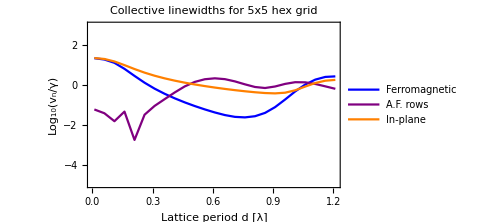

```mathematica
saveplt = True;
savesln = True;
linewidthplot[soln,polarizationmodes,gridname,atomnumx,atomnumy,"",saveplt,savesln]
```

compare square and hex grids

```mathematica
(*hexsoln = ToExpression[Import["soln_linewidth_v_period_hex5x6.txt"]];*)
hexsoln = ToExpression[Import["soln_linewidth_v_period_hex5x5.txt"]];
sqsoln = ToExpression[Import["soln_linewidth_v_period_square5x5.txt"]];
```

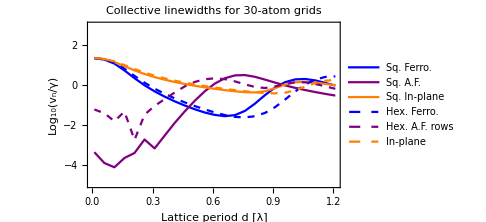

```mathematica
sln = Catenate[{sqsoln[[1;;3]],hexsoln}];
modes = {{None,{{None,"Sq. Ferro.",Blue},{None,"Sq. A.F.",Purple},{None,"Sq. In-plane",Orange},{None,"Hex. Ferro.",Directive[Blue,Dashed]},{None,"Hex. A.F. rows",Directive[Purple,Dashed]},{None, "In-plane",Directive[Orange,Dashed]}}}};
plt=linewidthplot[sln,modes,"",atomnumx,atomnumy,"Collective linewidths for 30-atom grids",False,False]
```

```mathematica
Export["linewidth_v_period_exactly30atoms_sq_hex.png",plt]
```

linewidth_v_period_exactly30atoms_sq_hex.png

```mathematica
hex5x5soln
```

{{{0.01,1.42397},{0.06,1.3462},{0.11,1.14233},{0.16,0.787728},{0.21,0.395708},{0.26,0.0406343},{0.31,-0.261198},{0.36,-0.520874},{0.41,-0.749045},{0.46,-0.95103},{0.51,-1.1331},{0.56,-1.30186},{0.61,-1.45477},{0.66,-1.58409},{0.71,-1.68103},{0.76,-1.71736},{0.81,-1.67307},{0.86,-1.51802},{0.91,-1.2362},{0.96,-0.853887},{1.01,-0.417787},{1.06,-0.0165076},{1.11,0.274578},{1.16,0.429757},{1.21,0.457788}},{{0.01,-3.01601},{0.06,-1.57037},{0.11,-1.50857},{0.16,-2.04837},{0.21,-2.37878},{0.26,-1.91305},{0.31,-1.39961},{0.36,-1.00529},{0.41,-0.618399},{0.46,-0.221135},{0.51,0.113593},{0.56,0.323003},{0.61,0.39133},{0.66,0.333232},{0.71,0.188625},{0.76,0.0189336},{0.81,-0.11523},{0.86,-0.160187},{0.91,-0.0787183},{0.96,0.061474},{1.01,0.136611},{1.06,0.130956},{1.11,0.0513367},{1.16,-0.0714032},{1.21,-0.196091}},{{0.01,1.4471},{0.06,1.37547},{0.11,1.21522},{0.16,1.00315},{0.21,0.793774},{0.26,0.611907},{0.31,0.458719},{0.36,0.3283},{0.41,0.214964},{0.46,0.114779},{0.51,0.0251244},{0.56,-0.0560053},{0.61,-0.130058},{0.66,-0.197831},{0.71,-0.260164},{0.76,-0.317219},{0.81,-0.368403},{0.86,-0.411632},{0.91,-0.439406},{0.96,-0.427622},{1.01,-0.32532},{1.06,-0.11677},{1.11,0.102559},{1.16,0.242233},{1.21,0.28366}}}

```mathematica
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afrowsmode,"A.F. rows",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes};
```

```mathematica
Manipulate[ListPlot[Re[evecs[[i]]],PlotStyle-> {{0,25},{-.5,.5}}],{i,Range[Length[evecs]]}]
```

## misc physics analysis

Why do the out-of-plane modes become very subradiant near λ = 0.7?

```mathematica
k=2π/λ;
```

Nearest- and next-to-nearest coupling terms:

```mathematica
Clear[k]
nn=ComplexExpand[Re[{1,0,0}.GdotP[{0,r,r},{1,0,0}]]]
```

```mathematica
1/(4π r)(Cos[√2 k r]/(√2)-Cos[√2 k √(r^2)]/(8 √2 k^2 r^2)-Sin[√2 k r]/(2 k π r))
```

```mathematica
nnn=ComplexExpand[Re[{1,0,0}.GdotP[{0,r,0},{1,0,0}]]]
```

```mathematica
1/(4 π r)(Cos[k r](1-1/(k^2 r^2))-Sin[k r]/(k r))
```

```mathematica
Collect[1/(4 π r)(Cos[k r](1-1/(k^2 r^2))-Sin[k r]/(k r))+1/(4π r)(Cos[√2 k r]/(√2)-Cos[√2 k r]/(8 √2 k^2 r^2)-Sin[√2 k r]/(2 k π r)),{1/(4π),1/r^2,1/r}]
```

((Cos[k r]+Cos[√2 k r]/(√2))/r+(-Cos[k r]/k^2-Cos[√2 k r]/(8 √2 k^2))/r^3+(-Sin[k r]/k-Sin[√2 k r]/(2 k π))/r^2)/(4 π)

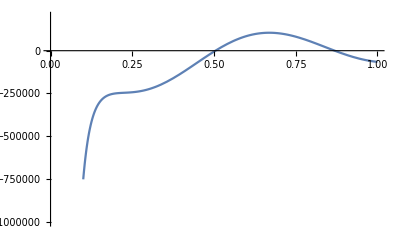

```mathematica
k=2π/λ;
Plot[(*1/(4 π)((Cos[k r]+Cos[√2 k r]/(√2))/r-(+Sin[k r]+Sin[√2 k r]/(2 π))/(k r^2)-(Cos[k r]-Cos[√2 k r]/(8 √2))/(k^2 r^3))/.r-> α λ*)ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]],{α,0.1,1},PlotRange->{-10^6,200000}]
```

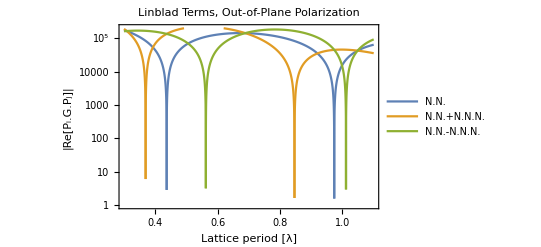

```mathematica
plt = LogPlot[{Abs[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],Abs[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]+ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]]],Abs[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]-ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]]]},{α,0.3,1.1},PlotStyle->Thin,PlotRange->{1,200000},PlotPoints->5000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Re[P_i.G.P_j]|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLegends->{"N.N.","N.N.+N.N.N.", "N.N.-N.N.N."}, PlotLabel->Style["Linblad Terms, Out-of-Plane Polarization",FontSize->12]]
```

```mathematica
(*Export["plot_nn_nnn_sqgrid_coupling.png",plt]*)
```

plot_nn_nnn_sqgrid_coupling.png

```mathematica
LogPlot[Abs[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","Re[P_i.G.P_j]"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

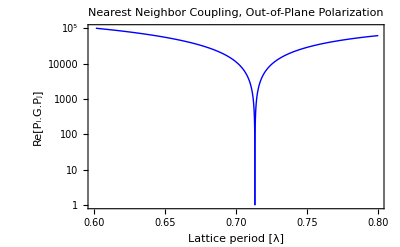

```mathematica
LogPlot[Abs[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","Re[P_i.G.P_j]"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

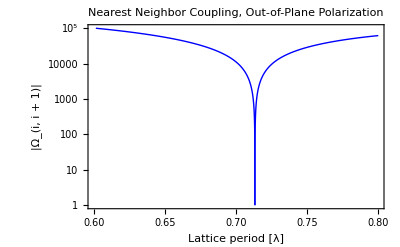

```mathematica
LogPlot[Abs[1/(4 π r)(Cos[k r](1-1/(k^2 r^2))-Sin[k r]/(k r))/.r-> α λ],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Ω_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

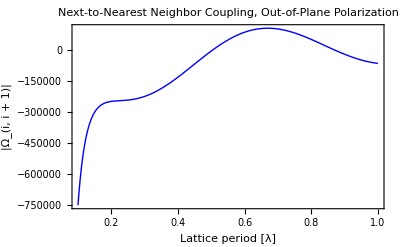

```mathematica
Plot[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,α λ},{1,0,0}]]],{α,0.1,1},PlotStyle-> Directive[Blue,Thin],(*PlotRange->{1,100000},*)(*PlotPoints->3000,*)Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Ω_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Next-to-Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

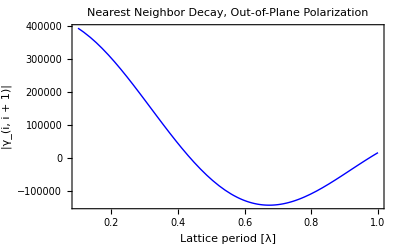

```mathematica
Plot[ComplexExpand[Im[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]],{α,0.1,1},PlotStyle-> Directive[Blue,Thin],PlotRange->All(*PlotPoints->3000*),Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|γ_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Decay, Out-of-Plane Polarization",FontSize->12]]
```

```mathematica
Clear[k];
ComplexExpand[{1,0,0}.GdotP[{rx,ry,rz},{1,0,0}]]
```

(3 rx^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 k^2 π (rx^2+ry^2+rz^2)^(5/2))-Cos[k √(rx^2+ry^2+rz^2)]/(4 k^2 π (rx^2+ry^2+rz^2)^(3/2))+(ry^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2))+(rz^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2))+(3 rx^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 k π (rx^2+ry^2+rz^2)^2)-Sin[k √(rx^2+ry^2+rz^2)]/(4 k π (rx^2+ry^2+rz^2))+ⅈ (-(3 rx^2 Cos[k √(rx^2+ry^2+rz^2)])/(4 k π (rx^2+ry^2+rz^2)^2)+Cos[k √(rx^2+ry^2+rz^2)]/(4 k π (rx^2+ry^2+rz^2))+(3 rx^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 k^2 π (rx^2+ry^2+rz^2)^(5/2))-Sin[k √(rx^2+ry^2+rz^2)]/(4 k^2 π (rx^2+ry^2+rz^2)^(3/2))+(ry^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2))+(rz^2 Sin[k √(rx^2+ry^2+rz^2)])/(4 π (rx^2+ry^2+rz^2)^(3/2)))

```mathematica
Together[]
```

Why does the ferromagnetic mode become increasingly subradiant as d becomes smaller, whereas the nearest neighbor coupling vanishes very sharply?

## radiation in the time domain

```mathematica
(*initialize the state vector. excite central 9 atoms in m=0 states*)
(*state = Array[Subscript[b, ##]&,dim];
excitedIdcs = Flatten@Table[(atomnum-1)/2+√atomnum i+j-1,{i,{-1,0,1}},{j,{-1,0,1}}];
state[[excitedIdcs]]=1; *)
```

```mathematica
centerIdx =Floor[√atomnum/2](√atomnum+1)+1 ; (*idx of the central atom*)
```

## tests

Check my grid mapping. 2D grid, but only one index to specify atoms.

#### square grid

```mathematica
atomnum = 25;
num = √atomnum; 
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
gridpts = Table[atom[i,False],{i,Range[num^2]}];
(*excited= Table[atom[i,True],{i,Flatten@Table[(atomnum-1)/2+√atomnum i+j-1,{i,{-1,0,1}},{j,{-1,0,1}}]}];*)
positions[pts_]:=Table[r[1,j],{j,pts}]
```

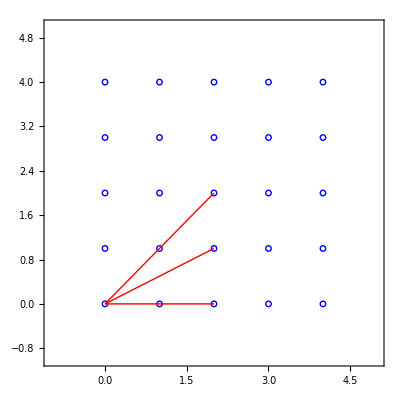

```mathematica
a=1;(*0.7;*)
showpos = {3,8,13};
Show[gridpts,positions[showpos],PlotRange->{{-a,a num},{-a,a num}},Frame->{True,True,False,False},Axes->False]
```

#### hex grid

```mathematica
atomnumx=5;
atomnumy =Floor[2/(√3)atomnumx+0.5]; 
a=1;
x[i_]:=Mod[i-1,atomnumx]+a/2 Mod[Floor[(i-1)/atomnumx],2];
y[i_]:=(√3)/2 Floor[(i-1)/atomnumx];
Subscript[r, i_,j_]={0,Mod[j-1,atomnumx]-Mod[i-1,atomnumx]+a/2(Mod[Floor[(j-1)/atomnumx],2]-Mod[Floor[(i-1)/atomnumx],2]),(√3)/2(Floor[(j-1)/atomnumx]-Floor[(i-1)/atomnumx])};
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{x[i],y[i]},0.05]}],Graphics[{Blue,Circle[a{x[i],y[i]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{x[i],y[i]},a{x[j],y[j]}}]}];
gridpts = Table[atom[i,False],{i,Range[atomnumx atomnumy]}];
positions[pts_]:=Table[r[1,j],{j,pts}];
```

```mathematica
Table[Mod[Floor[(i-1)/atomnumx],2],{i,Range[atomnumx atomnumy]}]
```

{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,1,1}

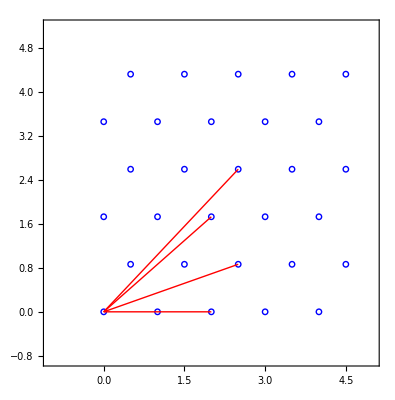

```mathematica
showpos = {3,8,13,18};
Show[gridpts,positions[showpos],PlotRange->{a{-1,atomnumx },a(√3)/2{-1,atomnumy}},Frame->{True,True,False,False},Axes->False]
```

```mathematica
Subscript[r, i_,j_]={0,Mod[j-1,atomnumx]-Mod[i-1,atomnumx]+a/2(Mod[Floor[(j-1)/atomnumx],2]-Mod[Floor[(i-1)/atomnumx],2]),(√3)/2(Floor[(j-1)/atomnumx]-Floor[(i-1)/atomnumx])};
```

```mathematica
r
```

{0,1,√3}